# A Wright-Fisher Model of host-pathogen coevolution

```mathematica
PlotOptions={ImageSize->{Automatic,300},Frame->True,FrameTicks->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,14],Background->White};
```

## The deterministic limit (difference equations)

Difference Equations

```mathematica
WH[1,t_]:=1-αH(X pP[t]+Y (1-pP[t]))
WH[2,t_]:=1-αH(X (1-pP[t])+Y pP[t])
WP[1,t_]:=1+αP(X pH[t]+Y (1-pH[t]))
WP[2,t_]:=1+αP(X (1-pH[t])+Y pH[t])
```

```mathematica
gH[t_]:=pH[t](WH[1,t]/(WH[1,t]pH[t]+WH[2,t](1-pH[t])))//FullSimplify
gP[t_]:=pP[t](WP[1,t]/(WP[1,t]pP[t]+WP[2,t](1-pP[t])))//FullSimplify
```

```mathematica
gH[t]-pH[t]//FullSimplify
```

((X-Y) αH (-1+pH[t]) pH[t] (-1+2 pP[t]))/(1-X αH+(X-Y) αH (pH[t]+pP[t]-2 pH[t] pP[t]))

```mathematica
gP[t]-pP[t]//FullSimplify
```

((X-Y) αP (-1+2 pH[t]) (-1+pP[t]) pP[t])/(-1-X αP+(X-Y) αP (pH[t]+pP[t]-2 pH[t] pP[t]))

Equilibrium and Stability

```mathematica
equi=Solve[{gH[t]==pH[t],gP[t]==pP[t]},{pH[t],pP[t]}]
```

{{pH[t]→0,pP[t]→0},{pH[t]→1,pP[t]→0},{pH[t]→1/2,pP[t]→1/2},{pH[t]→0,pP[t]→1},{pH[t]→1,pP[t]→1}}

```mathematica
jMtrx={{D[gH[t],pH[t]],D[gH[t],pP[t]]},{D[gP[t],pH[t]],D[gP[t],pP[t]]}}/.equi[[3]]//Simplify;
```

```mathematica
λs=FullSimplify[Eigenvalues[jMtrx]]
```

{(-4-√((X-Y)^2 αH (-2+(X+Y) αH) αP (2+(X+Y) αP))+(X+Y) (-2 αP+αH (2+(X+Y) αP)))/((-2+(X+Y) αH) (2+(X+Y) αP)),(-4+√((X-Y)^2 αH (-2+(X+Y) αH) αP (2+(X+Y) αP))+(X+Y) (-2 αP+αH (2+(X+Y) αP)))/((-2+(X+Y) αH) (2+(X+Y) αP))}

This can be rewritten as:
λ=1±((X-Y) √-1 √(α_H α_P(2-(X+Y)α_H)(2+(X+Y) α_P)))/((2-(X+Y)α_H)(2+(X+Y) α_P))

The magnitude of these is always greater than one. The eigenvalues are imaginary and hence the equilibrium characterized by unstable cycles.

The rate at which the cycles deviate from equilibrium is given by the magnitude of the eigenvalue.

```mathematica
λLen=Sqrt[1^2+(((X-Y) √-1 √(αH αP(2-(X+Y)αH)(2+(X+Y) αP)))/((2-(X+Y)αH)(2+(X+Y) αP)))^2];
```

```mathematica
λLen
```

√(1-((X-Y)^2 αH αP)/((2-(X+Y) αH) (2+(X+Y) αP)))

Numerical Solution

```mathematica
Clear[nSol]
nSol[tMax_,inits_,pars_]:=nSol[tMax,inits,pars]=Block[{out,τ},out={{pH0,pP0}/.inits};
For[τ=1,τ≤tMax,τ++,
AppendTo[out,{gH[t],gP[t]}/.pars/.{pH[t]->out[[-1,1]],pP[t]->out[[-1,2]]}]
];
out
]
```

```mathematica
gH[t]
```

(pH[t] (1-Y αH+(-X+Y) αH pP[t]))/(1-X αH+(X-Y) αH (pH[t]+pP[t]-2 pH[t] pP[t]))

```mathematica
TestPars={X->0.8,Y->0.4,αH->0.4,αP->0.4};
TestInits={pH0->0.56,pP0->0.44};
```

```mathematica
DetPlotAF[tMax_,inits_,pars_]:=Show[
(*Deterministic AF dynamics*)
ListLinePlot[nSol[tMax,inits,pars],PlotRange->{{0,1},{0,1}},PlotStyle->Black]/.Line[x_]:>{Arrowheads[Table[.05,{r,{2}}]],Arrow[x]},
(*Initial conditions*)
ListPlot[{{pH0,pP0}/.inits},PlotStyle->Red,PlotMarkers->{●,10}],PlotOptions,AspectRatio->1]
```

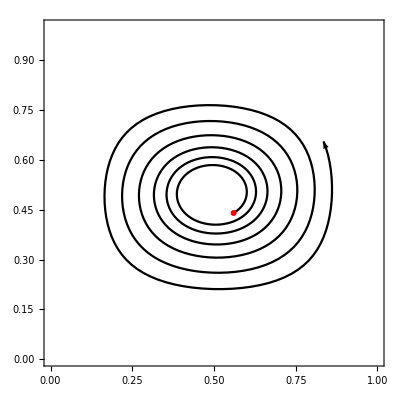

```mathematica
DetPlotAF[500,TestInits,TestPars]
Export[NotebookDirectory[]<>"Plots/WF_Det_AF.pdf",%,ImageResolution->300];
```

```mathematica
AvgH[tMax_,inits_,pars_]:=Block[{temp},
temp=2nSol[tMax,inits,pars][[;;,1]]*(1-nSol[tMax,inits,pars][[;;,1]]);
Table[Mean[temp[[1;;x]]],{x,1,tMax+1/.pars}]
]
```

```mathematica
DetPlotHet[tMax_,inits_,pars_]:=Show[
(*Heterozygosity Dynammics*)
ListLinePlot[2nSol[tMax,inits,pars][[;;,1]]*(1-nSol[tMax,inits,pars][[;;,1]]),PlotStyle->Black],
(*Initial Conditions*)
ListPlot[{2pH0(1-pH0)/.inits},PlotStyle->Red,PlotMarkers->{●,10}],
(*Avg H*)
ListLinePlot[AvgH[tMax,inits,pars],PlotStyle->Directive[Black,Dashed]]
,PlotRange->{0,0.5},PlotOptions,AspectRatio->0.75]
```

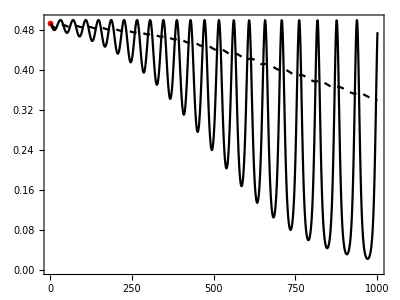

```mathematica
Show[DetPlotHet[1000,TestInits,TestPars]]
Export[NotebookDirectory[]<>"Plots/WF_Det_Het.pdf",%,ImageResolution->300];
```

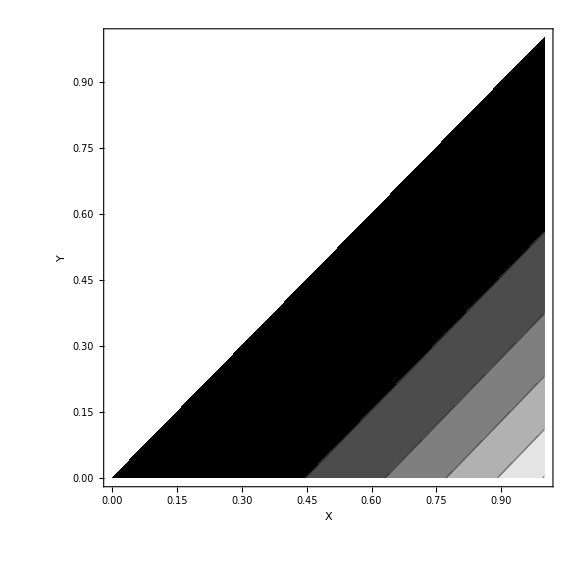

```mathematica
ContourPlot[λLen/.{α->0.2},{X,0,1},{Y,0,X},ColorFunction->GrayLevel,Frame->True,FrameLabel->{"X","Y"},FrameTicksStyle->Directive[Black,Bold,14], LabelStyle->Directive[Black,Bold, Large],ImageSize->Large]
```

Neutral Expectation

```mathematica
Hneut[n_,t_]:=0.5 (1-1/n)^t
```

As compared to the neutral expectation for the WF model
neutExp[κ_,t_]:=1/2 ⅇ^(-(2 t)/κ)

Gives the generation in the Moran model with the same expected heterozygosity as in the WF model at time tWF given the population size.

```mathematica
tMoSol[κ_,tWF_]:=Solve[0.5 (1-1/κ)^tWF==1/2 ⅇ^(-(2 tMo)/κ),tMo]//Flatten
```

## Simulations

Simulations

## Drawing Parameters

```mathematica
Clear[randPars]
randPars[nRun_,μIn_,tMaxIn_,nDemesIn_]:=randPars[nRun,μIn,tMaxIn,nDemesIn]=Block[{x,y,c,a,out,rep},out={};
For[c=1,c≤nRun,c++,
x=RandomReal[];y=RandomReal[{0,x}];a=RandomReal[{0,0.5}];
AppendTo[out,{}];
For[rep=0,rep≤6,rep++,
AppendTo[out[[-1]],{X->x,Y->y,α->a,tMax->tMaxIn,nDemes->nDemesIn,κ->Round[10^(2+rep*0.25),2],μ->μIn}];
];
];
out
]
```

```mathematica
parsList=randPars[50,0.00,500,1000];
temp=Flatten[Table[{run,rep,X,Y,α,tMax,nDemes,κ,μ}/.parsList[[run,rep]],{run,1,50},{rep,1,7}],1];
parsTable=PrependTo[temp,{"run","rep","X","Y","alpha","tMax","nDemes","kappa","mu"}];
Export[NotebookDirectory[]<>"WFSims_no_mu/pars.csv",parsTable];
```

## Running Simulations

```mathematica
export[run_,rep_]:=Block[{hostTab,pathTab},hostTab=simWF[parsList[[run,rep+1]]][[;;,;;,2]];pathTab=simWF[parsList[[run,rep+1]]][[;;,;;,3]];
 Export[NotebookDirectory[]<>"WFSims_no_mu/Host_run_"<>ToString[run]<>"_rep_"<>ToString[rep]<>".csv",hostTab];Export[NotebookDirectory[]<>"WFSims_no_mu/Path_run_"<>ToString[run]<>"_rep_"<>ToString[rep]<>".csv",pathTab];]
```

```mathematica
Clear[simWF]
simWF[pars_]:=simWF[pars]=Block[{out,d,t,WH,WP,nH1,nH2,nP1,nP2},out={};
WH[nPX_,nPY_]:=1-α(X nPX/κ+Y nPY/κ)/.pars; 
WP[nHX_,nHY_]:=1+α(X nHX/κ+Y nHY/κ)/.pars; 
For[d=1,d≤nDemes/.pars,d++,
If[Mod[d,500]==0,Print[d]];
AppendTo[out,{{0,Round[κ/2/.pars],Round[κ/2/.pars]}}];
For[t=1,t≤tMax/.pars,t++,
nH1=out[[-1,-1,2]];nH2=κ-out[[-1,-1,2]]/.pars;
nP1=out[[-1,-1,3]];nP2=κ-out[[-1,-1,3]]/.pars;
AppendTo[out[[-1]],{t,RandomVariate[BinomialDistribution[κ/.pars,(WH[nP1,nP2]nH1)/(WH[nP1,nP2]nH1+WH[nP2,nP1]nH2)]],RandomVariate[BinomialDistribution[κ/.pars,(WP[nH1,nH2]nP1 (1-μ/.pars)+WP[nH2,nH1]nP2(μ/.pars))/(WP[nH1,nH2]nP1+WP[nH2,nH1]nP2)]]}];
];
];
out//N
]
```

```mathematica
Clear[simWFAll]
simWFAll=Do[Print[{run,rep}];simWF[parsList[[run,rep+1]]];export[run,rep];,{run,1,50},{rep,0,6}]
```

### Explaining variation

```mathematica
TestPars={X->0.9,Y->0.89,tMax->200,nDemes->1000,κ->100};
TestPars2={X->0.1,Y->0.09,tMax->200,nDemes->1000,κ->100};
TestPars3={X->0.9,Y->0.8955757084820807,tMax->200,nDemes->1000,κ->100};
```

```mathematica
simWF[TestPars]
```

{{{0.,50.,50.},{1.,46.,44.},{2.,39.,48.},{3.,48.,52.},{4.,49.,42.},{5.,51.,42.},{6.,50.,35.},{7.,52.,28.},{8.,52.,32.},{9.,47.,29.},181,{191.,100.,0.},{192.,100.,0.},{193.,100.,0.},{194.,100.,0.},{195.,100.,0.},{196.,100.,0.},{197.,100.,0.},{198.,100.,0.},{199.,100.,0.},{200.,100.,0.}},998,{1}}
 |  |  |  |

```mathematica
simWF[TestPars2]
```

{{{0.,50.,50.},{1.,50.,57.},{2.,53.,56.},{3.,54.,52.},{4.,58.,54.},{5.,58.,55.},{6.,50.,45.},{7.,51.,41.},{8.,54.,44.},{9.,49.,45.},181,{191.,100.,0.},{192.,100.,0.},{193.,100.,0.},{194.,100.,0.},{195.,100.,0.},{196.,100.,0.},{197.,100.,0.},{198.,100.,0.},{199.,100.,0.},{200.,100.,0.}},998,{1}}
 |  |  |  |

```mathematica
simWF[TestPars3]
```

{{{0.,50.,50.},{1.,45.,47.},{2.,41.,51.},{3.,46.,57.},{4.,54.,56.},{5.,58.,58.},{6.,61.,54.},{7.,59.,52.},{8.,53.,52.},{9.,61.,53.},181,{191.,100.,0.},{192.,100.,0.},{193.,100.,0.},{194.,100.,0.},{195.,100.,0.},{196.,100.,0.},{197.,100.,0.},{198.,100.,0.},{199.,100.,0.},{200.,100.,0.}},998,{1}}
 |  |  |  |

```mathematica
{λLen/.TestPars,TestPars}
```

{0.0112091,{X→0.9,Y→0.89,tMax→200,nDemes→1000,κ→100}}

```mathematica
{λLen/.TestPars2,TestPars2}
```

{0.00502272,{X→0.1,Y→0.09,tMax→200,nDemes→1000,κ→100}}

```mathematica
{λLen/.TestPars3,TestPars3}
```

{0.00502272,{X→0.9,Y→0.895576,tMax→200,nDemes→1000,κ→100}}

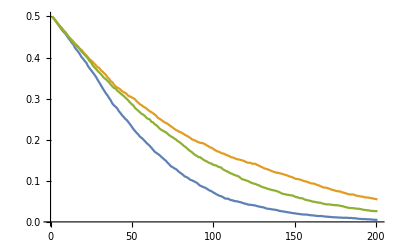

```mathematica
ListLinePlot[{Mean[Hdyn[TestPars]],Mean[Hdyn[TestPars2]],Mean[Hdyn[TestPars3]]}]
```

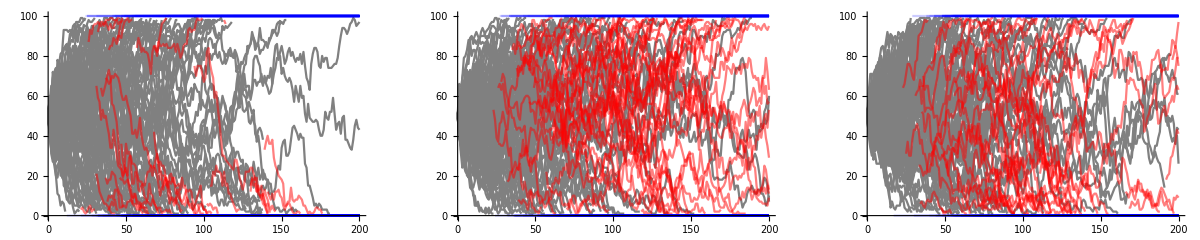

```mathematica
GraphicsRow[{NPlot[TestPars],NPlot[TestPars2],NPlot[TestPars3]},ImageSize->Full]
```

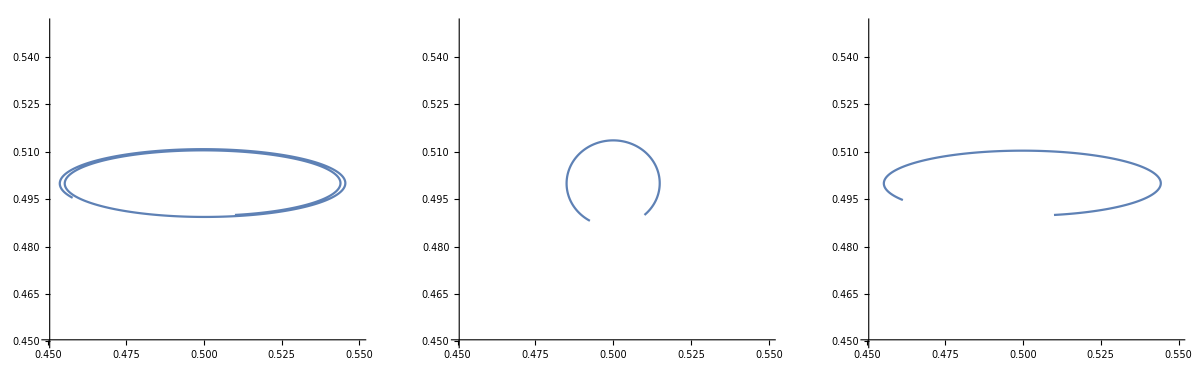

```mathematica
GraphicsRow[{ListLinePlot[nSol[1000,{pH0->0.51,pP0->0.49},TestPars],AspectRatio->1,PlotRange->{{0.45,0.55},{0.45,0.55}}],ListLinePlot[nSol[1000,{pH0->0.51,pP0->0.49},TestPars2],AspectRatio->1,PlotRange->{{0.45,0.55},{0.45,0.55}}],ListLinePlot[nSol[1000,{pH0->0.51,pP0->0.49},TestPars3],AspectRatio->1,PlotRange->{{0.45,0.55},{0.45,0.55}}]},ImageSize->Full]
```

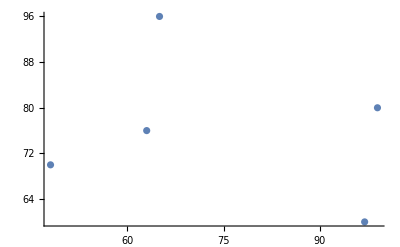

```mathematica
Select[Table[simWF[TestPars2][[deme,DirSel[TestPars2,deme],{1,2}]],{deme,51,60}],#≠{}&][[;;,1]]//ListPlot
```

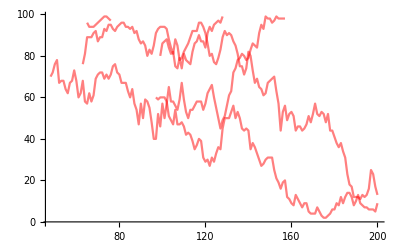

```mathematica
ListLinePlot[Select[Table[simWF[TestPars2][[deme,DirSel[TestPars2,deme],{1,2}]],{deme,51,60}],#≠{}&],PlotStyle->Directive[Red,Opacity[0.5]]]
```

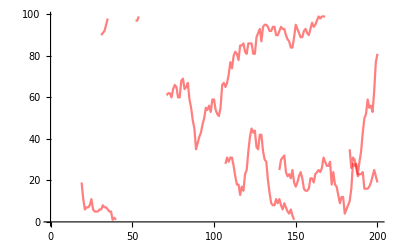

```mathematica
ListLinePlot[Select[Table[simWF[TestPars3][[deme,DirSel[TestPars3,deme],{1,2}]],{deme,101,120}],#≠{}&],PlotStyle->Directive[Red,Opacity[0.5]]]
```

Importing Runs

```mathematica
noMu=NotebookDirectory[]<>"Sims/WFSims_no_mu/";
(*Mu=NotebookDirectory[]<>"Sims/WFSims_mu/";*)
```

```mathematica
(*{"run","rep","X","Y","alpha","tMax","nDemes","kappa"}*)
Clear[pars]
pars[file_]:=pars[file]=Import[file<>"pars.csv"][[2;;]]
```

```mathematica
simPars[file_,run_,rep_]:=Block[{temp},temp=pars[file][[7*(run-1)+rep+1]];
{X->temp[[3]],Y->temp[[4]],α->temp[[5]],κ->temp[[8]](*,μ->temp[[-1]]*)}
]
```

Import data: Gives a 1000x501 matrix element i,j gives the number of hosts/parasites of type 1 in that deme i at generation j

```mathematica
Clear[repDataH,repDataP]
repDataH[file_,run_,rep_]:=repDataH[file,run,rep]=Import[file<>"Host_run_"<>ToString[run]<>"_rep_"<>ToString[rep]<>".csv"]
repDataP[file_,run_,rep_]:=repDataP[file,run,rep]=Import[file<>"Path_run_"<>ToString[run]<>"_rep_"<>ToString[rep]<>".csv"]
```

Processing

```mathematica
(*Both host and pathogen are polymorphic*)
Clear[CoevSel]
CoevSel[file_,run_,rep_,deme_]:=CoevSel[file,run,rep,deme]=Block[{data},
data=Transpose[{repDataH[file,run,rep][[deme]],repDataP[file,run,rep][[deme]]}];
Quiet[Flatten[Position[data,_?(#[[1]]≠0&&#[[1]]≠(κ/.simPars[file,run,rep])&&#[[2]]≠0&&#[[2]]≠(κ/.simPars[file,run,rep])&)],1]]
]
```

```mathematica
(*Host Polymorpic, Pathogen Fixed*)
Clear[DirSel]
DirSel[file_,run_,rep_,deme_]:=DirSel[file,run,rep,deme]=Block[{data},
data=Transpose[{repDataH[file,run,rep][[deme]],repDataP[file,run,rep][[deme]]}];
Quiet[Flatten[Position[data,_?(#[[1]]≠0&&#[[1]]≠(κ/.simPars[file,run,rep])&&(#[[2]]==0||#[[2]]==(κ/.simPars[file,run,rep]))&)],1]]
]
```

```mathematica
(*Host Fixed*)
Clear[Fixed]
Fixed[file_,run_,rep_,deme_]:=Fixed[file,run,rep,deme]=Block[{data},
data=Transpose[{repDataH[file,run,rep][[deme]],repDataP[file,run,rep][[deme]]}];
Quiet[Flatten[Position[data,_?((#[[1]]==0||#[[1]]==(κ/.simPars[file,run,rep]))&)],1]]
]
```

```mathematica
Clear[Hdyn]
Hdyn[file_,run_,rep_]:=Hdyn[file,run,rep]=2 repDataH[file,run,rep]/(κ/.simPars[file,run,rep])(1-repDataH[file,run,rep]/(κ/.simPars[file,run,rep]))
```

```mathematica
Hneut[file_,run_,rep_,t_]:=Hneut[κ/.simPars[file,run,rep],t]
```

```mathematica
BootstrapMean[data_,nBoot_]:=BootstrapMean[data,nBoot]=Block[{out,b},out={};
For[b=1,b≤nBoot,b++,
AppendTo[out,Mean[RandomChoice[data,Length[data]]]]
];
out]
```

Plotting

## Heterozygosity

```mathematica
HDynPlot[file_,run_,rep_]:=ListLinePlot[Mean[Hdyn[file,run,rep]]];
```

```mathematica
HDynPlot2[file_,rep_]:=ListLinePlot[Table[Mean[Hdyn[file,run,rep]],{run,1,15(*20*)}],PlotStyle->ColorData["CMYKColors"][(rep-1)/6],PlotRange->{0,0.5}];
```

```mathematica
HDynPlot3[file_,rep_]:=Show[HDynPlot2[file,rep],Plot[Hneut[κ/.simPars[file,1,rep],t],{t,0,500},PlotStyle->Directive[Black,Thick],PlotRange->{0,0.5}],PlotRange->All,Frame->True,FrameLabel->{"Time","H_coev"},LabelStyle->Directive[Black,Bold, Large],FrameTicksStyle->Directive[14],ImageSize->Large]
```

### Box Plot

```mathematica
HetBW[file_,t_]:=Block[{data,sigData,rep,point},sigData={};
point=Graphics[{EdgeForm[Black],White,Disk[Scaled[{0.5,0.5}],0.02]}];
data=Table[Mean[Hdyn[file,run,rep]][[t]]-Hneut[file,run,rep,t],{rep,1,7},{run,1,60}];
(*Which reps are signifcantly below 0*)
For[rep=1,rep≤7,rep++,
If[Mean[BootstrapMean[data[[rep]],10000]]+1.64 StandardDeviation[BootstrapMean[data[[rep]],10000]]<0,
AppendTo[sigData,{{rep,0.1}}],AppendTo[sigData,{{rep,0}}]]
];
Show[DistributionChart[data,ChartStyle->Table[ColorData["CMYKColors"][rep/6],{rep,0,6}]],ListPlot[Table[Transpose[{RandomReal[{rep-0.1,rep+0.1},60],data[[rep]]}],{rep,1,7}],PlotMarkers->point],ListPlot[sigData,PlotStyle->Table[ColorData["CMYKColors"][rep/6],{rep,0,6}],PlotMarkers->✶],ListLinePlot[{{0.2,0},{8,0}},PlotStyle->Directive[Black]],PlotRange->{{0.5,7.5},{-0.5,0.1}},Frame->True,(*FrameLabel->{"Log_10[κ]","ΔH"},*)FrameTicks->{{True,False},{Table[{rep,2+(rep-1)*0.5},{rep,1,7}],False}},LabelStyle->Directive[Black,Bold, 16],FrameTicksStyle->Directive[14],ImageSize->Large]
]
```

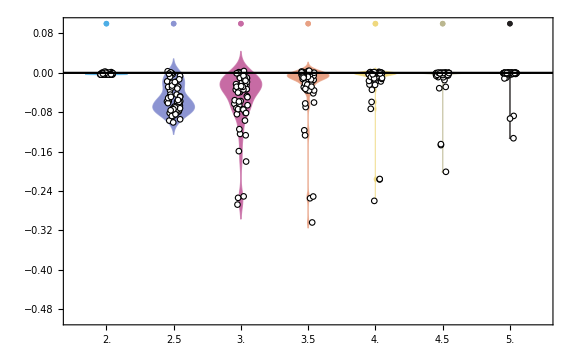

```mathematica
HetBW[noMu,0,500]
```

```mathematica
Export[NotebookDirectory[]<>"Plots/WF_HetBW_Mu.gif",HetBW[Mu,500],ImageResolution->300];
```

### Mean Fitting Function

#### LOESS Mean Smoothing

Project data onto the X=Y line.

```mathematica
Clear[dataNew]
dataNew[data_]:=dataNew[data]=Transpose[{Cos[Abs[ArcTan[data[[;;,2]]/data[[;;,1]]]-π/4]]*Sqrt[Total[Transpose[data^2]]],Sin[ArcTan[data[[;;,2]]/data[[;;,1]]]-π/4]*Sqrt[Total[Transpose[data^2]]]}]
```

A gaussian weighting of the data  near the point xNew along the X=Y line

```mathematica
Clear[weights]
weights[xNew_,αW_,data_]:=weights[xNew,αW,data]=Exp[-(dataNew[data][[;;,1]]-xNew)^2/(2 αW^2)];
```

Find the weighted mean and standard deviation and standard error.

```mathematica
Clear[meanNew]
meanNew[xNew_,αW_,data_]:=meanNew[xNew,αW,data]=Total[weights[xNew,αW,data]dataNew[data][[;;,2]]]/Total[weights[xNew,αW,data]]
```

```mathematica
SDNew[xNew_,αW_,data_]:=Sqrt[Total[weights[xNew,αW,data]*(dataNew[data][[;;,2]]-meanNew[xNew,αW,data])^2]/Total[weights[xNew,αW,data]]]
```

```mathematica
SENew[xNew_,αW_,data_]:=SDNew[xNew,αW,data]/Sqrt[Total[weights[xNew,αW,data]]]
```

The rolling average fit along the X+Y line (rotated plot)

```mathematica
Clear[RollFit]
RollFit[αW_,npts_,data_]:=RollFit[αW,npts,data]=Table[{x,meanNew[x,αW,data]},{x,Sqrt[2*0.5^2]/(npts+2),Sqrt[2*0.5^2]-Sqrt[2*0.5^2]/(npts+2),Sqrt[2*0.5^2]/(npts+2)}];
```

Projecting back into the original coordinates.

```mathematica
RollFitOld[αW_,npts_,data_]:=Transpose[{Cos[ArcTan[(RollFit[αW,npts,data][[;;,2]])/(RollFit[αW,npts,data][[;;,1]])]+π/4]Sqrt[(RollFit[αW,npts,data][[;;,2]])^2+(RollFit[αW,npts,data][[;;,1]])^2],Sin[ArcTan[(RollFit[αW,npts,data][[;;,2]])/(RollFit[αW,npts,data][[;;,1]])]+π/4]Sqrt[(RollFit[αW,npts,data][[;;,2]])^2+(RollFit[αW,npts,data][[;;,1]])^2]}]
```

```mathematica
Bootstrap[data_,dummy_]:=Bootstrap[data,dummy]=RandomChoice[data,Length[data]]
```

#### Plotting

```mathematica
Clear[data]
data[file_,t_]:=data[file,t]=Table[{Hneut[file,run,rep,t],Mean[Hdyn[file,run,rep]][[t]]},{rep,0,6},{run,1,50}]
```

```mathematica
data[noMu,200];
```

```mathematica
Clear[sigΔH]
ΔHrep[file_,run_,rep_,t_]:=Hdyn[file,run,rep][[t]]-Hneut[file,run,rep,t]
sigΔH[file_,t_]:=sigΔH[file,t]=Block[{outSig,outNotSig,run,rep,CIU,CIL},outSig={};outNotSig={};
For[rep=0,rep≤6,rep++,
AppendTo[outSig,{}];AppendTo[outNotSig,{}];
For[run=1,run≤50,run++,
CIU=Mean[ΔHrep[file,run,rep,t]]+(*1.96*)2.64 StandardDeviation[BootstrapMean[ΔHrep[file,run,rep,t],1000]];
CIL=Mean[ΔHrep[file,run,rep,t]]-(*1.96*)2.64 StandardDeviation[BootstrapMean[ΔHrep[file,run,rep,t],1000]];
If[CIU>0&&CIL<0,AppendTo[outNotSig[[-1]],{Hneut[file,run,rep,t],Mean[Hdyn[file,run,rep]][[t]]}],AppendTo[outSig[[-1]],{Hneut[file,run,rep,t],Mean[Hdyn[file,run,rep]][[t]]}]]
];
If[outSig[[rep]]=={},AppendTo[outSig[[rep]],{-0.01,-0.01}]];
If[outNotSig[[rep]]=={},AppendTo[outNotSig[[rep]],{-0.01,-0.01}]];
];
{outNotSig,outSig}
]
```

```mathematica
Table[tMoSol[10^(2+0.25 rep),200],{rep,0,6}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{{tMo→100.503},{tMo→100.282},{tMo→100.158},{tMo→100.089},{tMo→100.05},{tMo→100.028},{tMo→100.016}}

```mathematica
moranMean[t_]:=Import[NotebookDirectory[]<>"MoranMean_"<>ToString[t]<>".csv"];
```

Comparing the WF model at time tWF to the moran model at time tMoran

```mathematica
Clear[ModelComparison]
ModelComparison[file_,tWF_,tMoran_]:=Show[
(*Neutral *)
Plot[x,{x,0,0.5},PlotStyle->Directive[Black,Dashed]],
(*Points*)
ListPlot[sigΔH[file,tWF][[1]],PlotStyle->Table[Lighter[ColorData["CMYKColors"][rep/6]],{rep,0,6}],PlotMarkers->○],ListPlot[sigΔH[file,tWF][[2]],PlotStyle->Table[Directive[ColorData["CMYKColors"][rep/6]],{rep,0,6}],PlotMarkers->●],
(*Bootstrap lines*)
ListLinePlot[Table[RollFitOld[0.1,40,Bootstrap[Flatten[data[file,tWF],1],x]],{x,0,1000}],PlotStyle->Directive[Green,Opacity[0.01]]],
(*Mean*)
ListLinePlot[RollFitOld[0.1,40,Flatten[data[file,tWF],1]],PlotStyle->Directive[Darker[Green],Thick]],
(*Moran Mean*)
ListLinePlot[moranMean[tMoran],PlotStyle->Red],
PlotOptions,AspectRatio->1,PlotRange->{{0,0.5},{0,0.5}}]
```

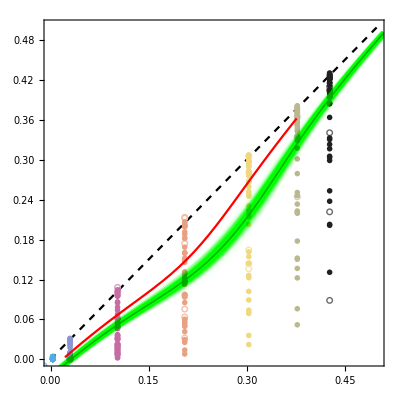

```mathematica
ModelComparison[noMu,500,500]
```

What if we compare when the expected neutral expectations are equal.

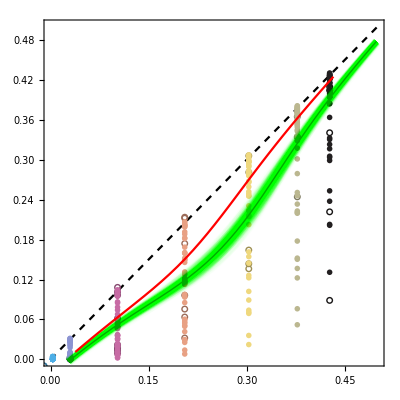

```mathematica
ModelComparison[noMu,500,250]
```

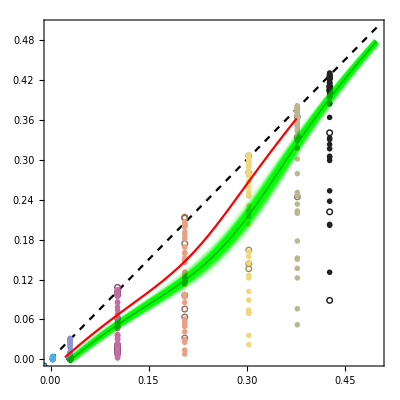

```mathematica
ModelComparison[noMu,500,500]
Export[NotebookDirectory[]<>"Plots/ModelComparison.pdf",%,ImageResolution->300];
```

```mathematica
κLegWF=PointLegend[Table[ColorData["CMYKColors"][rep/6],{rep,0,6}],Table[ToString[Round[10^(2+0.25rep)]]<>" ("<>ToString[Round[Length[sigΔH[noMu,500][[1,rep+1]]]/Length[sigΔH[noMu,500][[2,rep+1]]]*100]]<>"%)",{rep,0,6}],LegendFunction->"Frame",LegendLabel->Text[Style["κ",14,Bold]]]
Export[NotebookDirectory[]<>"Plots/kappaLegWF.pdf",κLegWF];
```

```mathematica
ModelCompLegend=LineLegend[{{Black,Dashed},Red,Darker[Green]},{"Neutral Expectation","Moran Model","WF Model"}]
```

```mathematica
Export[NotebookDirectory[]<>"Plots/ModelCompLegend.pdf",ModelCompLegend,ImageResolution->300];
```

### λ Length

The correlation between the leading eigenvalue λ and ΔH for a given population size

```mathematica
Clear[R2,lm]
λLenPlot[file_,rep_,t_]:=Block[{data,lm},data=Table[{λLen/.{αH->α,αP->α}/.simPars[file,run,rep],Mean[Hdyn[file,run,rep]][[t]]-Hneut[file,run,rep,t]},{run,1,50}];
lm=LinearModelFit[data,x,x];
R2[rep,t]=lm["RSquared"];
Show[Plot[lm[x],{x,Min[data[[;;,1]]],Max[data[[;;,1]]]},PlotRange->All,PlotStyle->ColorData["CMYKColors"][(rep-1)/6]],ListPlot[data,PlotStyle->ColorData["CMYKColors"][(rep-1)/6]],PlotRange->All]
]
```

The correlation between the leading eigenvalue λ and ΔH for across all population sizes

```mathematica
λLenPlot2[file_,t_]:=Show[Table[λLenPlot[file,r,t],{r,0,6}],PlotRange->{-0.5,0.1},Epilog->Table[Text[Style[(*"R^2="<>*)ToString[Round[R2[rep,t],0.001]],14,ColorData["CMYKColors"][rep/6]],Scaled[{0.9,0.1+(0.5-0.1)/7(8-rep)}]],{rep,0,6}],PlotRange->{-0.5,0.1},PlotOptions]
```

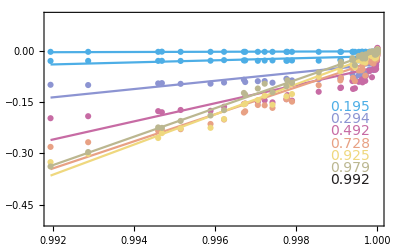

```mathematica
λLenPlot2[noMu,500]
```

```mathematica
Export[NotebookDirectory[]<>"Plots/lambdaLenPlotWF.pdf",λLenPlot2[noMu,500]];
```

## Allele Frequency

```mathematica
test[noMu,1,0]
```

{1}
 |  |  |  |

```mathematica
(*Doesn't work with mutation*)
NPlot[file_,run_,rep_]:=Show[{ListLinePlot[Select[Table[Transpose[{CoevSel[file,run,rep,deme],1/(κ/.simPars[file,run,rep])repDataH[file,run,rep][[deme,CoevSel[file,run,rep,deme]]]}],{deme,1,100}],#≠{}&],PlotStyle->Gray],ListLinePlot[Select[Table[Transpose[{DirSel[file,run,rep,deme],1/(κ/.simPars[file,run,rep])repDataH[file,run,rep][[deme,DirSel[file,run,rep,deme]]]}],{deme,1,100}],#≠{}&],PlotStyle->Red],ListLinePlot[Select[Table[Transpose[{Fixed[file,run,rep,deme],1/(κ/.simPars[file,run,rep])repDataH[file,run,rep][[deme,Fixed[file,run,rep,deme]]]}],{deme,1,100}],#≠{}&],PlotStyle->Blue]},PlotRange->All,Frame->True,(*FrameLabel->{"time","Allele Frequency"},*)LabelStyle->Directive[Black,Bold, 18],FrameTicksStyle->Directive[14],ImageSize->Large]
```

```mathematica
(*Works with mutation*)
NPlot2[file_,run_,rep_]:=Show[{ListLinePlot[Select[Table[Transpose[{CoevSel[file,run,rep,deme],1/(κ/.simPars[file,run,rep])repDataH[file,run,rep][[deme,CoevSel[file,run,rep,deme]]]}],{deme,1,100}],#≠{}&],PlotStyle->Directive[Gray,Opacity[0.2]]],ListLinePlot[Flatten[Map[Split[#,#2[[1]]-#1[[1]]<2&]&,Select[Table[Transpose[{DirSel[file,run,rep,deme],1/(κ/.simPars[file,run,rep])repDataH[file,run,rep][[deme,DirSel[file,run,rep,deme]]]}],{deme,1,100}],#≠{}&]],1],PlotStyle->Directive[Red,Opacity[0.5]]],ListLinePlot[Select[Table[Transpose[{Fixed[file,run,rep,deme],1/(κ/.simPars[file,run,rep])repDataH[file,run,rep][[deme,Fixed[file,run,rep,deme]]]}],{deme,1,100}],#≠{}&],PlotStyle->Directive[Blue,Opacity[0.2]]]},PlotOptions]
```

```mathematica
simPars[noMu,1,2]
```

{X→0.268502,Y→0.065726,α→0.236447,κ→316}

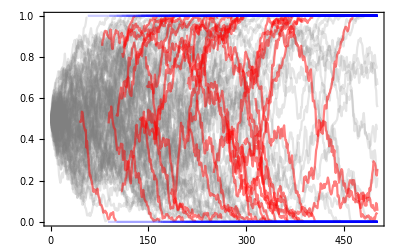

```mathematica
NPlot2[noMu,1,2]
```

```mathematica
Export[NotebookDirectory[]<>"Plots/WF_AF.pdf",NPlot2[noMu,1,2],ImageResolution->300];
```